## Hankel function mapped on to the surface of a sphere

Spherical Harmonics and the two components of the Hankel functions

```mathematica
l=20;
m=5;
f=Re;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[SphericalHarmonicY[l,m,#4,#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH1[m,√(l(l+1))*#4] )*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH2[m,√(l(l+1))*#4])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
```

-Graphics3D-

-Graphics3D-

```mathematica
l=20;
m=5;
f=Re;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH1[m,√(l(l+1))*#4] )*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->400]
```

-Graphics3D-

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/hankel_1.pdf",%15,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/hankel_1.pdf

```mathematica
l=20;
m=5;
f=Re;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH2[m,√(l(l+1))*#4])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->400]
```

-Graphics3D-

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/hankel_2.pdf",%5,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/hankel_2.pdf

## Legendre function

Spherical Harmonics and the two components of the Legendre functions

```mathematica
l=20;
m=5;
f=Re;
t=1;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[SphericalHarmonicY[l,m,#4,#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[√((2l+1)/(4Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]+ ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[√((2l+1)/(4Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
```

-Graphics3D-

-Graphics3D-

```mathematica
l=20;
m=5;
f=Re;
t=1;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[√((2l+1)/(4Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]+ ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->400]
```

-Graphics3D-

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/fld_1.pdf",%25,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/fld_1.pdf

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/fld_1.pdf",%6,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/fld_1.pdf

```mathematica
l=20;
m=5;
f=Re;
t=1;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[√((2l+1)/(4Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->400]
```

-Graphics3D-

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/fld_2.pdf",%6,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/fld_2.pdf

```mathematica
Export["/Users/vigeesh/work/ms/fldcode2015/figures/fld_2.pdf",%6,"PDF"]
```

/Users/vigeesh/work/ms/fldcode2015/figures/fld_2.pdf

```mathematica
(*Using a different normalizing factor*)
l=20;
m=5;
f=Re;
t=1;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[SphericalHarmonicY[l,m,#4,#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(-l)^m*((l-m)!)/((l+m)!)*(LegendreP[l,m,Cos[#4 ]]+ ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(-l)^m*((l-m)!)/((l+m)!)*(LegendreP[l,m,Cos[#4 ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
```

-Graphics3D-

-Graphics3D-

```mathematica
l=20;
m=1;
f=Re;
gradients=ColorData["RedGreenSplit"];
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH1[m,√(l(l+1))*#4] )*Exp[I*m*#5] - √((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]+ ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},
ColorFunction->(gradients[.5+f[(HankelH2[m,√(l(l+1))*#4])*Exp[I*m*#5] - √((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[#4 ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[#4] ])*Exp[I*m*#5]]]&),Mesh->{17},MeshStyle->Opacity[0.2],
Boxed->False,Axes->False,ColorFunctionScaling->False,PlotPoints->200,SphericalRegion->True,ViewAngle->.3,ImageSize->100]
```

```mathematica
(* http://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html *)
ClearAll["Global`*"]
l=30;
m=10;
θ=π;
NIntegrate[Re[HankelH1[m,√(l(l+1))*2]*Exp[I *m* ϕ] ],{ϕ,0,π},Exclusions->{0,π},PrecisionGoal->12,MaxRecursion->12]//Timing
(*NIntegrateProfile@NIntegrate[Re[HankelH1[m,√(l(l+1))*θ]*Exp[I m ϕ] ],{θ,0.001,π},Method->{"GlobalAdaptive","SingularityHandler"->"DuffyCoordinates"}]*)
(*sampledPoints=Reap[NIntegrate[Re[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ],{θ,0,π},{ϕ,0,2π},Exclusions->{{0,π},{0,π}},Method->{"LocalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}},EvaluationMonitor:>Sow[θ]]][[2,1]];
ListPlot[Transpose[{sampledPoints,Range[Length[sampledPoints]]}]]
*)
(*NIntegrate[Re[HankelH1[m,√(l(l+1))*θ]*Exp[I m ϕ] ],{θ,0,π,0,π},{ϕ,0,2π,0,2π},Method->{"GlobalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}}]*)
(*(∫_0)^(2π)((∫_0)^π (HankelH1[m,√(l(l+1))*θ] )*Exp[I*m*ϕ] - √((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[θ]]+ ((2*I)/Pi)LegendreQ[l,m,Cos[θ] ])*Exp[I*m*ϕ]ⅆθ) ⅆϕ

(∫_0)^(2π)((∫_0)^π (HankelH2[m,√(l(l+1))*θ])*Exp[I*m*ϕ] - √((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[θ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[θ] ])*Exp[I*m*ϕ]ⅆθ) ⅆϕ*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.85469×10^-18 and 2.98874×10^-17 for the integral and error estimates.

{3.11534,-5.85469×10^-18}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {θ, ϕ} = {0.0000101162, 0.0000202323}. NIntegrate obtained 0.0000173926 and 8.33977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {θ, ϕ} = {0.0000101162, 0.0000442008}. NIntegrate obtained 0.0000521779 and 0.0000250193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {θ, ϕ} = {0.0000101162, 0.0000681692}. NIntegrate obtained 0.0000869631 and 0.0000416988 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

$Aborted

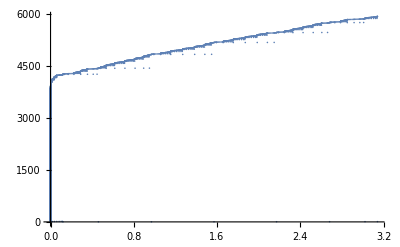

```mathematica
sampledPoints=Reap[NIntegrate[Re[HankelH1[m,√(l(l+1))*θ]*Exp[I m ϕ] ],{θ,0,π,0,π},{ϕ,0,2π},Method->{"LocalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}},EvaluationMonitor:>Sow[θ]]][[2,1]];
ListPlot[Transpose[{sampledPoints,Range[Length[sampledPoints]]}]]
```

```mathematica
NIntegrate[Re[HankelH1[m,√(l(l+1))*θ]*Exp[I m ϕ] ],{θ,0.1,π},{ϕ,0.1,2π},Method->{"DuffyCoordinates","Corners"->All}]
```

$Aborted

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -9.02938×10^26 + 9.25795×10^27\ ⅈ and 1.18979×10^28 for the integral and error estimates.

-9.02938×10^26+9.25795×10^27 ⅈ

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 4.77167×10^34 - 1.16753×10^35\ ⅈ and 1.57074×10^35 for the integral and error estimates.

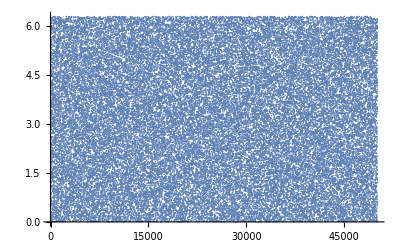

0.0591789+0.100429 ⅈ

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
θ=π/2;
k=0;
NIntegrate[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ,{θ,0,0,π},{ϕ,0,2π,2π},Method->"MonteCarlo",PrecisionGoal->20]
tbl=Reap[NIntegrate[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ,{θ,0,0,π},{ϕ,0,2π,2π},Method->"MonteCarlo",PrecisionGoal->20,EvaluationMonitor:>Sow[ϕ]]][[2,1]];
ListPlot[tbl,PlotRange->All]
NSum[HankelH1[m,√(l(l+1))*π/2]*Exp[I *m* ϕ] ,{ϕ,0,π,π/100}]

(*NIntegrate[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ,{θ,0,0,π},{ϕ,0,2π,2π},Method->"GaussKronrodRule",WorkingPrecision->20,PrecisionGoal->12]
tbl=Reap[NIntegrate[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ,{θ,0,0,π},{ϕ,0,2π,2π},Method->"GaussKronrodRule",WorkingPrecision->20,PrecisionGoal->12,EvaluationMonitor:>Sow[ϕ]]][[2,1]];
ListPlot[tbl,PlotRange->All]*)
```

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
NSum[NSum[HankelH1[m,√(l(l+1))*θ]*Exp[I *m* ϕ] ,{θ,π/10000,π,π/10000}],{ϕ,0,2π,π/10000}]
```

NSum::nsnum: Summand (or its derivative) HankelH1[m, √l\ (l + 1)\ θ]\ Exp[ⅈ\ m\ ϕ] is not numerical at point θ = 3.14191.

SequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

2.74224×10^18-1.81732×10^28 ⅈ

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
ϕ=π/2;
NIntegrate[N[HankelH1[m,√(l(l+1))θ]*Exp[I m ϕ]] ,{θ,0,π},Exclusions->{0},Method->{"PrincipalValue","SingularPointIntegrationRadius"->π/1000}]
N[√((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[θ ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[θ] ])*Exp[I*m*ϕ]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.92286×10^-225}. NIntegrate obtained -0.119613 + 9.5619202057201570714816922356998432078176660903665259864760161321×10^251498\ ⅈ and 9.5619202057201570714816922356998432078176660903665259864760161321×10^251498 for the integral and error estimates.

-0.119613+9.56192020572016×10^251498 ⅈ

-5.3804×10^-15 (-6.01896×10^11 (-1.+Cos[θ]^2)^5 (143.-58630. Cos[θ]^2+3.78164×10^6 Cos[θ]^4-9.07592×10^7 Cos[θ]^6+1.06642×10^9 Cos[θ]^8-6.96728×10^9 Cos[θ]^10+2.69191×10^10 Cos[θ]^12-6.27125×10^10 Cos[θ]^14+8.62297×10^10 Cos[θ]^16-6.42496×10^10 Cos[θ]^18+1.99512×10^10 Cos[θ]^20)-(0.+0.63662 ⅈ) (-1/((-1.+Cos[θ]^2)^10)0.00360489 (1.-1. Cos[θ]^2)^5 (-1.05699×10^18 Cos[θ]+1.44543×10^20 Cos[θ]^3-6.13559×10^21 Cos[θ]^5+1.2702×10^23 Cos[θ]^7-1.55616×10^24 Cos[θ]^9+1.25447×10^25 Cos[θ]^11-7.1042×10^25 Cos[θ]^13+2.95056×10^26 Cos[θ]^15-9.25264×10^26 Cos[θ]^17+2.23408×10^27 Cos[θ]^19-4.20543×10^27 Cos[θ]^21+6.2123×10^27 Cos[θ]^23-7.20991×10^27 Cos[θ]^25+6.54494×10^27 Cos[θ]^27-4.59577×10^27 Cos[θ]^29+2.44669×10^27 Cos[θ]^31-9.54733×10^26 Cos[θ]^33+2.57562×10^26 Cos[θ]^35-4.2929×10^25 Cos[θ]^37+3.33118×10^24 Cos[θ]^39)+6.01896×10^11 (1.-1. Cos[θ]^2)^5 (143.-58630. Cos[θ]^2+3.78164×10^6 Cos[θ]^4-9.07592×10^7 Cos[θ]^6+1.06642×10^9 Cos[θ]^8-6.96728×10^9 Cos[θ]^10+2.69191×10^10 Cos[θ]^12-6.27125×10^10 Cos[θ]^14+8.62297×10^10 Cos[θ]^16-6.42496×10^10 Cos[θ]^18+1.99512×10^10 Cos[θ]^20) (-0.5 Log[1.-1. Cos[θ]]+0.5 Log[1.+Cos[θ]])))

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {θ, ϕ} = {3.35758×10^-11, 6.28319}. NIntegrate obtained 9.17207×10^113 - 1.65809×10^113\ ⅈ and 9.30942×10^113 for the integral and error estimates.

9.17207×10^113-1.65809×10^113 ⅈ

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

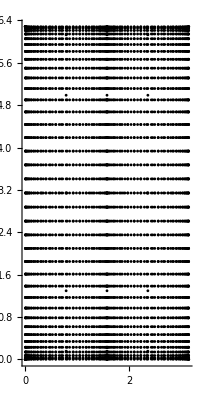

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
NIntegrate[N[HankelH1[m,√(l(l+1))θ]*Exp[I m ϕ]] ,{θ,0,0,π},{ϕ,0,2π},Method->{"GlobalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}},PrecisionGoal->10]
(*tbl=Reap[NIntegrate[N[HankelH1[m,√(l(l+1))θ]*Exp[I m ϕ]] ,{θ,0,π},{ϕ,0,2π},Method->{"GlobalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0},EvaluationMonitor:>Sow[{θ,ϕ}]]][[2,1]];
Graphics[{PointSize[0.005],Point/@N[tbl]},Axes->True]*)
tbl=Reap[NIntegrate[N[HankelH1[m,√(l(l+1))θ]*Exp[I m ϕ]] ,{θ,0,π},{ϕ,0,2π},Method->{"GlobalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}},WorkingPrecision->10,EvaluationMonitor:>Sow[{θ,ϕ}]]][[2,1]];
Graphics[{PointSize[0.005],Point/@N[tbl]},Axes->True]
```

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
Manipulate[
Plot[Re[N[HankelH1[m,√(l(l+1))θ]*Exp[I m ϕ]] ],{ϕ,-2π,2π}],{θ,-π,π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {6.2831852543501440696317632484324197661429423078516265377402305603}. NIntegrate obtained 1.08339×10^20 - 7.29799×10^20\ ⅈ and 1.05931×10^26 for the integral and error estimates.

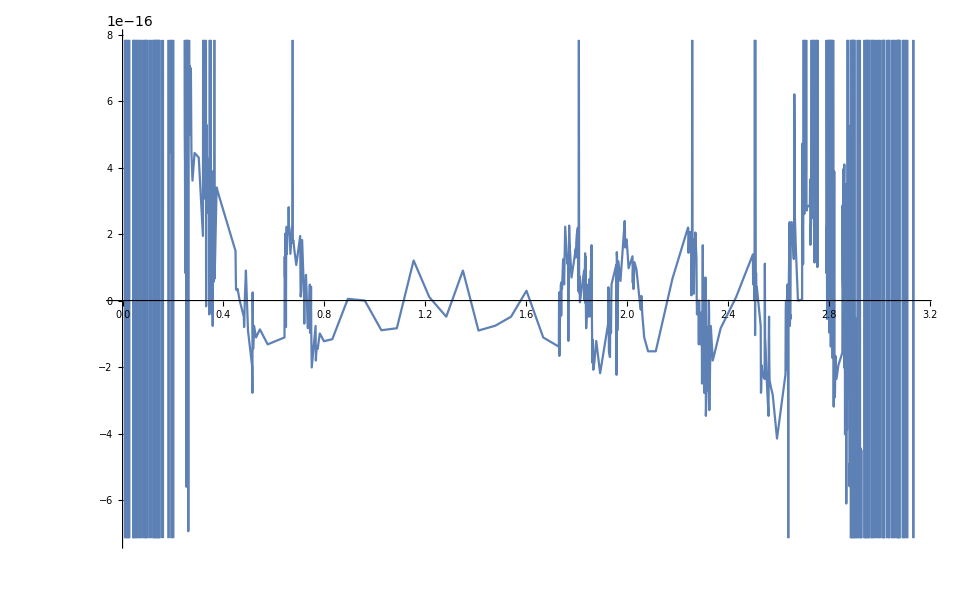

```mathematica
ClearAll["Global`*"]
l=30;
m=10;
Plot[Re[NIntegrate[N[HankelH1[m,√(l(l+1))*θ]*Exp[I*m*ϕ] - √((2l+1)/(2Pi)((l-m)!)/((l+m)!))*(LegendreP[l,m,Cos[θ]]- ((2*I)/Pi)LegendreQ[l,m,Cos[θ] ])*Exp[I*m*ϕ]] ,{ϕ,0,2π}]],{θ,0,π}]
```